```mathematica
TrigToExp[ArcTanh[x]]
```

-1/2 Log[1-x]+1/2 Log[1+x]

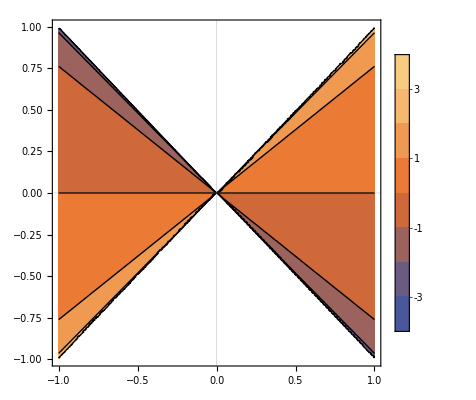

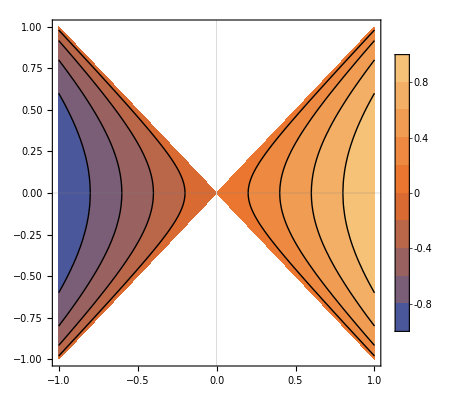

```mathematica
ContourPlot[ArcTanh[t/x],{x,-1,1},{t,-1,1},RegionFunction->Function[{x,t},Abs[t]<Abs[x]],PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
ContourPlot[Piecewise[{{√(x^2-t^2), x≥0}, {-√(x^2-t^2), x≤0}}],{x,-1,1},{t,-1,1},RegionFunction->Function[{x,t},Abs[t]<Abs[x]],PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
```

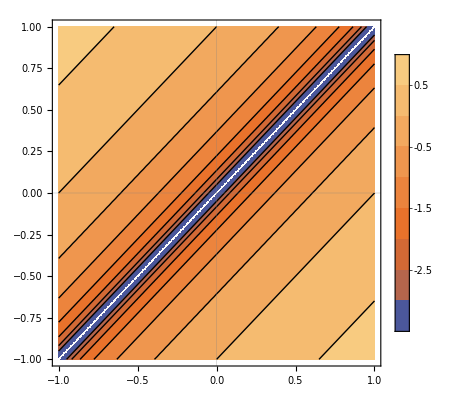

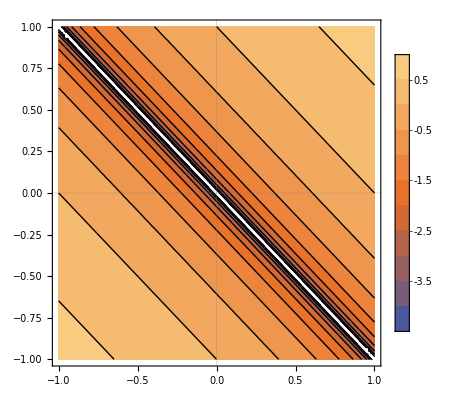

```mathematica
ContourPlot[+1/2 Log[(x-t)^2],{x,-1,1},{t,-1,1},(*RegionFunction->Function[{x,t},Abs[t]<Abs[x]],*)PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
ContourPlot[+1/2 Log[(x+t)^2],{x,-1,1},{t,-1,1},(*RegionFunction->Function[{x,t},Abs[t]<Abs[x]],*)PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
```

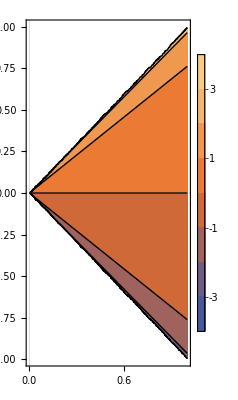

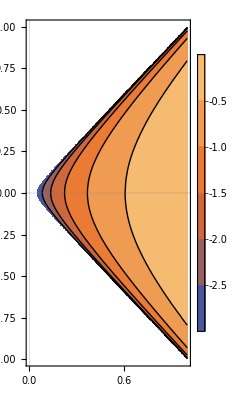

```mathematica
ContourPlot[ArcTanh[t/x],{x,0,1},{t,-1,1},RegionFunction->Function[{x,t},Abs[t]<x],PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
ContourPlot[1/2 Log[(x^2-t^2)],{x,0,1},{t,-1,1},RegionFunction->Function[{x,t},Abs[t]<x],PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
```

```mathematica
FullSimplify[TrigToExp[ArcTanh[t/x]-1/2 Log[(x^2-t^2)]],Assumptions->x>0&&-t<x&&t<x]
```

Log[1/(-t+x)]

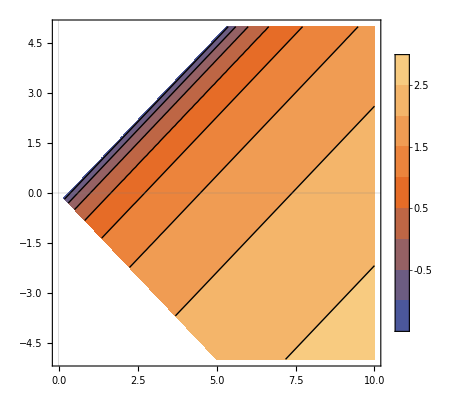

```mathematica
ContourPlot[Log[-t+x],{x,0,10},{t,-5,5},RegionFunction->Function[{x,t},Abs[t]<x],PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
```

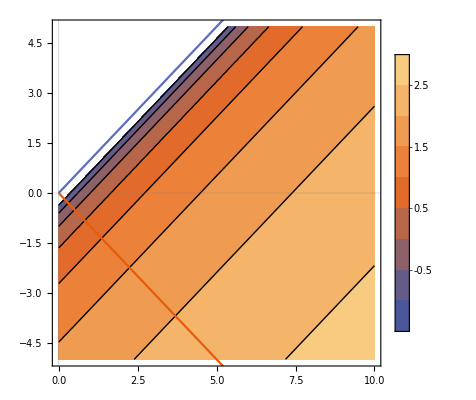

```mathematica
Show[ContourPlot[Log[-t+x],{x,0,10},{t,-5,5},RegionFunction->Function[{x,t},t<x],PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic],Plot[{-x,+x},{x,0,10},PlotTheme->"Scientific",AspectRatio->Automatic]]
```